## This notebook details analytical calculations to complement the paper “A shear-induced limit on bacterial surface adhesion in fluid flow” Author: Edwina Yeo, edwina.yeo.14@ucl.ac.uk Section 1: Calculation of mean orientation vector and nematic order parameter far from surface [SI section 2]

```mathematica
(*Validate that there is zero mean orientation eq.S10*)
Solve[{-nx/per+(1/2+b/4)ny==0,-ny/per-(1/2-b/4)nx==0},{nx,ny}]
```

{{nx→0,ny→0}}

```mathematica
(* Q tensor solve*) 
EE={{0,1/2},{1/2,0}};  (* Rate of strain*)
W={{0,1/2},{-1/2,0}}; (* Rate of rotation*)
Q={{Q11,Q12},{Q12,Q22}}; (* Q tensor*)

ppppE={{Q12/2, 1/8},{1/8,Q12/2}}; (*Closure for pp:D*)
(*Eq S13 *)
EQ=b*(EE.(Q+IdentityMatrix[2]/2)+(Q+IdentityMatrix[2]/2).EE)+W.(Q)-(Q).W-2*b*ppppE-4/per*Q//FullSimplify

(*Solve algebraic equations to give eq.S16*)

solq=Solve[{-(4 Q11)/per+Q12==0,-(4 Q12)/per+1/4 (b-2 Q11+2 b Q11+2 (1+b) Q22)==0,-Q12-(4 Q22)/per==0},{Q11,Q12,Q22}]
```

{{-(4 Q11)/per+Q12,-(4 Q12)/per+1/4 (b-2 Q11+2 b Q11+2 (1+b) Q22)},{-(4 Q12)/per+1/4 (b-2 Q11+2 b Q11+2 (1+b) Q22),-Q12-(4 Q22)/per}}

{{Q11→(b per^2)/(4 (16+per^2)),Q12→(b per)/(16+per^2),Q22→-(b per^2)/(4 (16+per^2))}}

## Section 2: Calculation of mean orientation vector in boundary layer [SI section 4]

```mathematica
(*eq. S30*)

sol=Solve[{-nx/per+(1/2+b/4)ny-Vs*Qxy*A==0,-ny/per-(1/2-b/4)nx-Vs*(Qyy+1/2)*A==0},{nx,ny}](* Here A=1/eps d\rho/dy*)
sol[[1]][[1]][[2]]//FullSimplify (*nx, eq S31*)
sol[[1]][[2]][[2]]//FullSimplify (*ny eq S31*)
```

{{nx→(2 per (2 A per Vs+A b per Vs+8 A Qxy Vs+4 A per Qyy Vs+2 A b per Qyy Vs))/(-16-4 per^2+b^2 per^2),ny→(4 (2 A per Vs-2 A per^2 Qxy Vs+A b per^2 Qxy Vs+4 A per Qyy Vs))/(-16-4 per^2+b^2 per^2)}}

(2 A per (8 Qxy+(2+b) per (1+2 Qyy)) Vs)/(-16+(-4+b^2) per^2)

(4 A per (2+(-2+b) per Qxy+4 Qyy) Vs)/(-16+(-4+b^2) per^2)

```mathematica
(*Now insert values of the nematic order tensor from above*)
Qyy=solq[[1]][[3]][[2]];
Qxy=solq[[1]][[2]][[2]];
sol[[1]][[1]][[2]]//FullSimplify (*nx, eq S32*)
sol[[1]][[2]][[2]]//FullSimplify (*ny eq S32*)
```

(A per^2 (64+48 b+4 per^2-b^2 per^2) Vs)/((16+per^2) (-16+(-4+b^2) per^2))

(4 A per (32+(-2+b) (-1+b) per^2) Vs)/((16+per^2) (-16+(-4+b^2) per^2))

Defining the Effective Peclet number

```mathematica
A=-1  (*set gradient to be equal to -1 to account for minus in eq S33*)
Peeff[Vs_,per_,b_]=(sol[[1]][[2]][[2]]*Vs)^(-1)//FullSimplify (*eq S33*)
(*(Peeff[Vs_,per_,b_]=((16+per^2) (16+(4-b^2) per^2))/(4 per (32+(2+(3-b) b) per^2) Vs^2)//FullSimplify (*Manually removing a minus from top and bottom*)*)
Peeff[Vs,per,0]//FullSimplify (*Confirm value for circular bacteria *)
```

-1

-((16+per^2) (-16+(-4+b^2) per^2))/(4 per (32+(-2+b) (-1+b) per^2) Vs^2)

(4+per^2)/(2 per Vs^2)

Defining  the Dimensional diffusion coeff.

```mathematica
Deff[gam_,dr_,Vs_,b_]=(Peeff[V/(gam L),gam/dr,b]/(gam*L*L))^(-1)//FullSimplify (* eq 19 *)
Deff[gam,dr,Vs,0]//FullSimplify (* Diffusivity for spherical bacteria, when dr>>gam when this is approximately Vs^2/(2dr)*)
```

(4 dr (32 dr^2+(-2+b) (-1+b) gam^2) V^2)/((16 dr^2+gam^2) (16 dr^2-(-4+b^2) gam^2))

(2 dr V^2)/(4 dr^2+gam^2)

#### Plotting flux as shear rate and beta vary

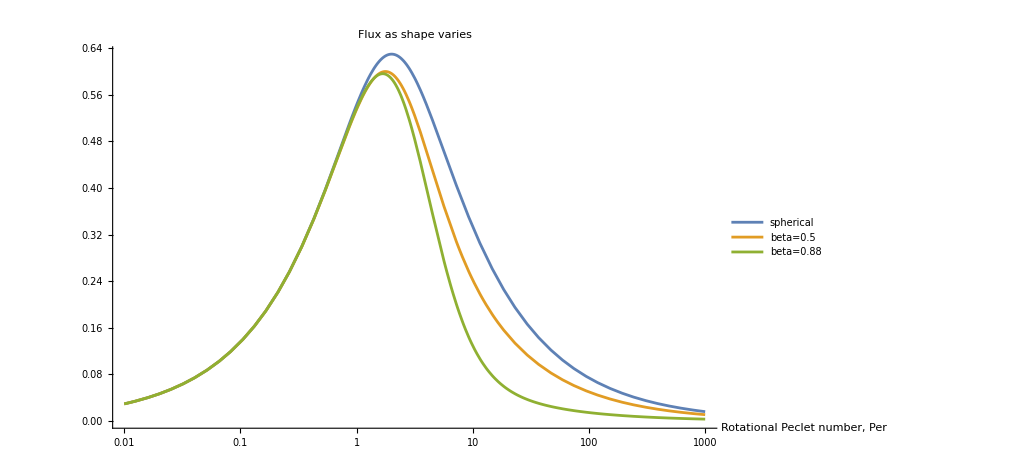

```mathematica
J[Vs_,per_,b_]=Peeff[Vs,per,b]^(-2/3);
LogLinearPlot[{J[1,per,0],J[1,per,0.35],J[1,per,0.88]},{per,0.01,1000},PlotLegends->{"spherical","beta=0.5","beta=0.88"},PlotLabel->"Flux as shape varies",AxesLabel->{"Rotational Peclet number, Per",""}] (* shows that flux is less for elongated bacteria with biggest difference at largest Per*)
```